```mathematica
FullSimplify[DSolve[y'[x]+y[x]/5 == ⅇ^(-x/5)Cos[x],y[x],x]]
```

{{y[x]→ⅇ^(-x/5) (C[1]+Sin[x])}}

```mathematica
y[x_]:=ⅇ^(-x/5) Sin[x]
```

```mathematica
FullSimplify[D[y[x],x]]
```

1/5 ⅇ^(-x/5) (5 Cos[x]-Sin[x])

```mathematica
FullSimplify[D[y[x],{x,2}]]
```

-2/25 ⅇ^(-x/5) (5 Cos[x]+12 Sin[x])

```mathematica
ya[x_]:=ⅇ^(-x/5) Sin[x]
```

```mathematica
dyadx[x_]:=1/5 ⅇ^(-x/5) (5 Cos[x]-Sin[x])
```

```mathematica
d2yadx2[x_]:=-2/25 ⅇ^(-x/5) (5 Cos[x]+12 Sin[x])
```

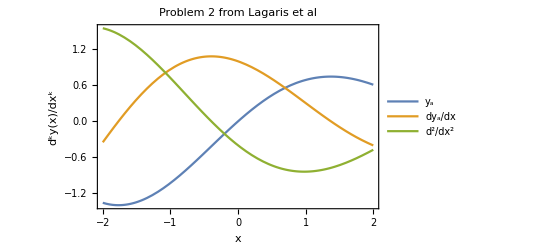

```mathematica
Plot[{ya[x],dyadx[x],d2yadx2[x]},{x,-2,2},AxesLabel->{"x","d^ky(x)/dx^k"},PlotLegends->{"y_a","dy_a/dx","d^2/dx^2"},PlotLabel->"Problem 2 from Lagaris et al",Frame->True]
```